```mathematica
If[!NumberQ[makePallette],NotebookEvaluate[NotebookDirectory[]~~"visualVocabDefs.nb"],NotebookEvaluate[NotebookDirectory[]~~"vvClear.nb"]];
```

## Inside Correlation

Correlation is a way to find patterns embedded in a large set of data, this notebook shows some of the details of the calculation.

```mathematica
TableForm[{{Hyperlink["CrossCorrelation",{"vvInsideCorr.nb","labelSigCorr2"},BaseStyle->mathColor],labelSigCorr2}}]
```

| Testing the correlation between various signals

This notebook contains further exploration of the ListCorrelate[ ] function.

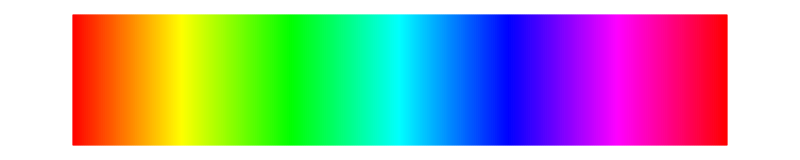

```mathematica
specLine
```

Say a known pattern of binary +/-1 numbers is embedded somewhere in a large data set. For example, the pattern of numbers highlighted in yellow might be hidden somewhere in the long stream of numbers highlighted in green. The goal is to find if the yellow sequence occurs within the data, and if so, to locate it. The figure below diagrams the method of correlation.

```mathematica
Column[{Image[-Graphics-,ImageSize->800] ,Style["Correlation can help to find a marker hidden inside a larger sequence",captionStyle]},Alignment->Center](* 1dimCorrelation.ai *)
```

-Graphics-
Correlation can help to find a marker hidden inside a larger sequence

The binary signal in green is shown with a seven-symbol embedded marker, highlighted in yellow. The process of correlation multiplies corresponding elements of the signal by the marker, and sums. The marker shifts to the right and the process repeats, creating the sequence of sums shown on the right in blue. The sum is largest when the marker is aligned with itself (because all the terms are positive, as occurs in the diagram at the shift R_(j+n)). Thus the shift with the largest correlation-sum (in this case shift j+n), is the largest term in the blue vector and points towards the embedded marker in the data sequence.

```mathematica
specLine
```

-Graphics-

More formally, the (cross) correlation between two signals x and y with shift j can be defined directly or in terms of the inner product. For each possible shift j, the correlation is

R_xy(j)=∑_(k=-∞)^∞ x(k) y(j+k)

When the correlation R_xy(j) is large, x and y point in (nearly) the same direction. If R_xy(j) is small (near zero), x and y (shifted by j) are nearly orthogonal. The correlation can also be interpreted in terms of similarity or closeness: large R_xy(j) mean that x and y are similar (close to each other) while small R_xy(j) mean they are different (far from each other). Because there are many possible j values, correlation shifts the y sequence (in time or space) and calculates how well they match (multiplying point by point and summing) at each shift. Hence correlation can be interpreted as a collection of inner products, one for each shift. When the sum is small, they are not much alike; when the sum is large, many terms are similar. This equation can be read as a recipe for the calculation of correlation. Choose a shift j and take the inner product, i.e., shift the signal y by j and then multiply point by point times x over all possible elements. The sum of the elements is the cross-correlation. Repeat for all possible j. Because the two signals do not need to be the same length, they are given different names: the kernel and the signal. For example, the cross correlation between a kernel {m,n} and a signal {a,b,c,d,e} is:

```mathematica
ListCorrelate[{m,n},{a,b,c,d,e},{-1,1},{0,0}]
```

{a n,a m+b n,b m+c n,c m+d n,d m+e n,e m}

while the cross correlation between the kernel {a,b,c,d,e} and a signal {m,n} is:

```mathematica
ListCorrelate[{a,b,c,d,e},{m,n},{-1,1},{0,0}]
```

{e m,d m+e n,c m+d n,b m+c n,a m+b n,a n}

The last pair of arguments in the ListCorrelate function (i.e. {-1, 1}, {0, 0}) indicate how end conditions are handled: in this case, zeros are padded onto both the front and end of the kernel and signal whenever needed. Because of this padding, there are as many terms in the cross correlation as the sum of the number of terms in the signal plus the number of terms in the kernel, minus one (in this case Length[{m,n}]+Length[{a,b,c,d,e}]-1=6). Other options can be given for other end conditions. Sometimes it is more useful to do no padding and sometimes it is useful to pad the signal and kernel circularly (to replace missing values with corresponding values from the opposite end of the sequence). In both these cases the length of the correlation is Max[Length[x],Length[y]], and examples are given here. Observe that the two sequences ListCorrelate[kernel,signal] and ListCorrelate[signal,kernel] are the same, except that the order of the output sequence is reversed.

```mathematica
specLine
```

-Graphics-

Here are some examples with more interesting signals:

```mathematica
labelSigCorr2="Testing the correlation between various signals";
infoSigCorr2="Select two signals from the chooser boxes. One is called the 'kernel' (left plot) and the other is called the 'signal' (middle plot). The cross correlation is shown in the right plot.\n\nObserve that the order of the signals is irrelevant: for example, the cross-correlation between a pulse train and single pulse is the same as the cross correlation between a single pulse and the pulse train.\n\nObserve that the two noise signals do not correlate well with any signal (other than themselves).\n\nObserve that the square and the triangle correlare almost as well as the square with itself (this is because they have the same basic period).\n\nAny signal correlated with a pulse gives back the signal.";Manipulate[GraphicsRow[{ListLinePlot[allSigs[[kernel]],Filling->Axis,PlotLabel->"Kernel: "~~sigNames[[kernel]]],ListLinePlot[allSigs[[signal]],Filling->Axis,PlotLabel->"Signal: "~~sigNames[[signal]]],ListLinePlot[ListCorrelate[allSigs[[kernel]],allSigs[[signal]],{-1,1},{0,0}],Filling->Axis,PlotLabel->"Cross-Correlation",PlotRange->All]},ImageSize->850],Row[{Control[{{kernel,5,""},Thread[Range[numSigs]->sigNames],ControlType->SetterBar}],Spacer[10],Control[{{signal,7,""},Thread[Range[numSigs]->sigNames],ControlType->SetterBar}],Spacer[10],info[infoSigCorr2]}],FrameLabel->Style[labelSigCorr2,Medium],TrackedSymbols->{signal,kernel},SaveDefinitions->True]
```

A collection of different signals appear above along with their correlations. When a train of pulses is correlated with a single pulse, the correlation reproduces the pulse once for each spike. When the pulse is correlated with a sinusoid, the correlation smears the pulse and inverts it with each undulation. When two different random signals are correlated, the output is modestly sized (and pretty random) because the two random sequences were chosen independently. Notice that when a random noise signal is correlated with itself, there is a large spike in the middle, indicated the shift j where the sequence is perfectly aligned with itself. Try these out (and more) above. Observe that when x=y (i.e., the kernel and the signal are the same), the largest value of the correlation occurs at a shift j=0. In the examples that are periodic, note that the distance between successive peaks of the correlation is directly related to the periodicity in the input.

One useful situation is when x and y are two copies of the same signal, but displaced in time. The variable j shifts y and at some shift j* they become aligned. At this j*, x[k] is the same as y[k+j*] and the product is positive everywhere: hence, when summed via the inner product, R_xy[j*] achieves its largest value. Thus the maximum value of the correlation occurs at shift j* where x[k]=y[k+j*], where the signals are closest, where the angle between them is zero. Correlation is an ideal tool for aligning signals in time.

A special case that can be very useful is when the two signals x and y happen to be the same. In this case, R_xx[j] = < x[k], x[k+j]> is called the autocorrelation of x. For any x, the largest value of the autocorrelation always occurs at j=0, that is, when there is no shift. This is particularly useful when x is periodic since then R_xx[j] has peaks at values of j that correspond precisely to the period. For example, when autocorrelating the periodic spike train with itself, the output has a series of peaks that are precisely one period apart. Similarly, when the input is a sinusoid with frequency of 12 oscillations per window (as in the above figure), the autocorrelation has peaks that are (approximately) 8 samples apart, which is the period of the sine wave (the period of the sinusoid is 100 samples/12 oscillations ~ 8 samples per oscillation).

Of course, correlation also can be used in two dimensions, and the formula is just two independent copies of the one dimensional formula. There are now two shift parameters i and j in two directions, and the sum is taken over all shifts in both directions. At any point {s,t} the cross correlation is:

R_xy[s,t]=∑_(i=-∞)^∞ ∑_(j=-∞)^∞ x[i,j] y[s+i,t+j]

More examples of the uses of correlation and autocorrelation in the application of correlation methods to the thread counting problem.